```mathematica
(*** DATA-DRIVEN PREDICTIONS ***)
```

```mathematica
(** FPR **) 
(* monitor error rates (empirical) dependency on window *)
```

```mathematica
(* automated *) 
getMonValues[dataDirPathForSeshNum[All], "FPR"]
```

{0.010586,0.001484,0.000467,0.000388,0.000271,0.000193,0.000115,0.000115,0.000114,0.000114,0.000038,0.000038,0.000038,0.000038,0.000037,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
(* generated from Session 4, det1 in the data repository -- 1hz, fpr = fnr = 0.1 *) 
(* empirical - monitor FPR by window size, from mon1 (2751 frames) *) 
empFPRbyWinSizeMon1 = ListLinePlot[{{2, 0.010109} ,{3, 0.001163}, {4,0},{5,0},{6,0},{7,0},{8,0},{9,0},{10,0}}, PlotLabel->"Empirical FPR of monitor", AxesLabel->{"Monitor window size (mon1, 2.7k frames)", "FPR"}, PlotStyle->Dashing[{0.01, 0.03}]];
```

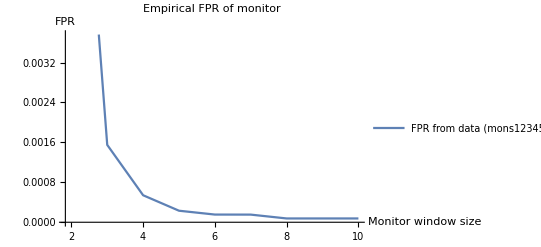

```mathematica
(* empirical - monitor FNR by window size, from mons12345 (13755 frames)  *)
empFPRbyWinSizeMons12345 = ListLinePlot[{{2, 0.010964} ,{3, 0.001550}, {4,0.000541},{5,0.000231},{6,0.000154},{7,0.000153},{8,0.000076},{9,0.000076},{10,0.000076}}, PlotLabel->"Empirical FPR of monitor", AxesLabel->{"Monitor window size", "FPR"},  PlotLegends->{"FPR from data (mons12345, 13.7k frames)"}]
```

```mathematica
(** FNR **)
```

{0.201409,0.284999,0.358476,0.423147,0.480576,0.53085,0.576453,0.61784,0.65734,0.692441,0.721449,0.749419,0.77381,0.795633,0.816231,0.8325,0.847522,0.860479,0.870064,0.879467,0.887072,0.894829,0.900802,0.908985,0.917598,0.925217,0.928571,0.928328,0.927632}

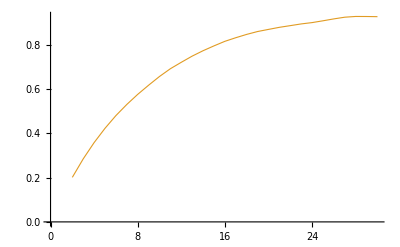

```mathematica
(* automated *) 
(* all sessions 4-7 *) 
getMonValues[dataDirPathForSeshNumPostCorr[All], "FNR"]
estFNRChartSesh4567 = ListLinePlot[Inner[List, Range[2,30], getMonValues[dataDirPathForSeshNumPostCorr[All], "FNR"], List], PlotStyle->{ColorData[97,"ColorList"][[2]], Thickness[0.002](*Darker@Blue,Dotted*)}(*, PlotLegends->{"Data estimate (7.7 hrs)"}*)]
```

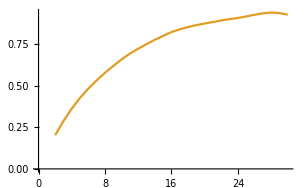
```mathematica
(* above but from before corrections: *) 
{0.202365,0.286893,0.361722,0.4265,0.482236,0.531182,0.576592,0.617842,0.656944,0.692051,0.720733,0.748507,0.774525,0.79798,0.821043,0.83703,0.851351,0.862613,0.872236,0.881081,0.89039,0.898649,0.905405,0.914607,0.924731,0.93311,0.938053,0.934641,0.925}
-Graphics-
```

{0.186486,0.266573,0.344624,0.411402,0.474277,0.529412,0.582746,0.632841,0.676357,0.716904,0.748927,0.777778,0.800481,0.820972,0.844262,0.853372,0.863924,0.869416,0.87594,0.879668,0.884259,0.890052,0.89759,0.908451,0.923729,0.93617,0.942857,0.934783,0.909091}

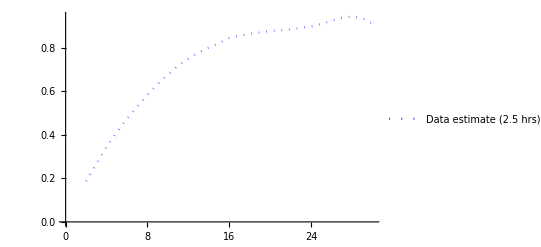

```mathematica
(* all session 6 *) 
getMonValues[dataDirPathForSeshNum[6], "FNR"]
estFNRChartSesh6= ListLinePlot[Inner[List, Range[2,30], getMonValues[dataDirPathForSeshNum[6], "FNR"], List],PlotStyle->{Lighter@Blue, Dotted}, PlotLegends->{"Data estimate (2.5 hrs)"}]
```

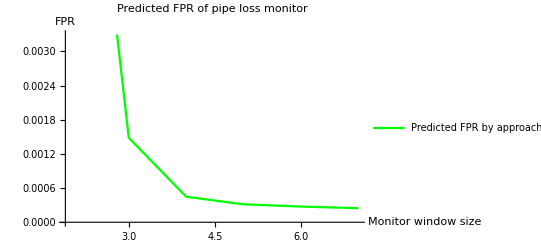

```mathematica
(*** APPROACH PREDICTIONS ***)


(* FPR/FNR estimates based on iter12345&det12345, priors/conditionals are from priorcond_iter12345_win6_stats.txt*) predFPRbyModSize = ListLinePlot[{{1, 0.010340023070913059} ,{2, 0.001483774261742787}, {3,0.00044828540282684716},{4,0.00031501632612945194},{5,0},{6,0},{7,0},{8,0},{9,0}, {10,0}}, PlotLabel->"Predicted FPR of monitor (FPR", AxesLabel->{"Modality window size", "FPR"},  PlotStyle->Green, PlotLegends->{"Predicted FPR by approach"}];
predFPRbyWinSize = ListLinePlot[{{2, 0.010340023070913059} ,{3, 0.001483774261742787}, {4,0.00044828540282684716},{5,0.00031501632612945194},{6,0.00027563453619774763},{7,0.00024669065927919963}(*,{8,0},{9,0},{10,0}*)}, PlotLabel->"Predicted FPR of pipe loss monitor", AxesLabel->{"Monitor window size", "FPR"},  PlotStyle->Green, PlotLegends->{"Predicted FPR by approach"}]
```

```mathematica
(* predicted - monitor FNR with modality size, cheaty *) 
betaERS := 1 - (1-alphaPI)(1 - alphaPI - pNChoPI)^d ;
predFNRbyModSize = ListLinePlot[Assuming[{alphaPI==0.1 (* cheating a bit *) , pNChoPI==0 , d == #}, {#, Simplify@betaERS}]& /@ Table[n, {n,1, 9, 1}], (* this is mon win - 1 *)
PlotLabel -> "Monitor FNR by monitor size - 1", AxesLabel -> {"Modality size (= monwin size - 1)", "Monitor FNR"},PlotStyle->Magenta];

(* predicted - monitor FNR with monitor window size, cheaty *) 
betaERSmonwin := 1 - (1-alphaPI)(1 - alphaPI - pNChoPI)^(monwin-1);
```

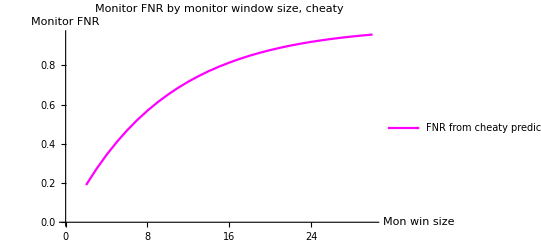

```mathematica
predFNRbyWinSizeCheatUpTo30 =ListLinePlot[Assuming[{alphaPI==0.1 (* cheating a bit *) , pNChoPI==0 , monwin== #}, {#, Simplify@betaERSmonwin}]& /@ Table[n, {n,2,30, 1}], (* this is mon win - 1 *)
PlotLabel -> "Monitor FNR by monitor window size, cheaty", AxesLabel -> {"Mon win size", "Monitor FNR"}, PlotStyle->Magenta, PlotLegends->{"FNR from cheaty prediction"}]
```

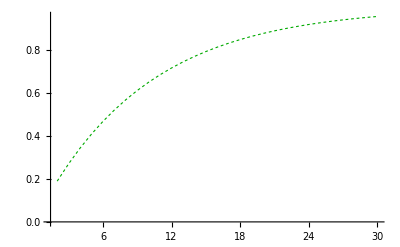

```mathematica
(* updated *) 
gtFNRChart =ListLinePlot[Assuming[{alphaPI==0.1 (* cheating a bit *) , pNChoPI==0 , monwin== #}, {#, Simplify@betaERSmonwin}]& /@ Table[n, {n,2,30, 1}], (* this is mon win - 1 *)
PlotStyle->{Dashing[0.005],Darker@Green, Thickness[0.002]}, (*PlotLegends->{"Ground-truth FNR"},*) PlotRange->All]
```

```mathematica
(** realistic predictions on individual detectors, iter12345 **) 

(* on det1 fpr *) 
predFNRbyWinSizeRealDet1 = ListLinePlot[Assuming[{alphaPI==0.125000  , pNChoPI==0 , monwin== #}, {#, Simplify@betaERSmonwin}]& /@ Table[n, {n,2,10, 1}], PlotLabel->"Empirical FNR of monitor", AxesLabel->{"Monitor window size", "FNR"},  PlotLegends->{"FNR from prediction"}, PlotStyle->Directive[Green,Dashing[{0.01, 0.03}]]];
```

```mathematica
(* on det2 fpr *) 
predFNRbyWinSizeRealDet2 = ListLinePlot[Assuming[{alphaPI==0.080000  , pNChoPI==0 , monwin== #}, {#, Simplify@betaERSmonwin}]& /@ Table[n, {n,2,10, 1}], PlotLabel->"Empirical FNR of monitor", AxesLabel->{"Monitor window size", "FNR"},  PlotLegends->{"FNR from prediction"}, PlotStyle->Directive[Green,Dashing[{0.01, 0.03}]]];
```

```mathematica
(* on det3 fpr *) 
predFNRbyWinSizeRealDet3 = ListLinePlot[Assuming[{alphaPI==0.120000  , pNChoPI==0 , monwin== #}, {#, Simplify@betaERSmonwin}]& /@ Table[n, {n,2,10, 1}], PlotLabel->"Empirical FNR of monitor", AxesLabel->{"Monitor window size", "FNR"},  PlotLegends->{"FNR from prediction"}, PlotStyle->Directive[Green,Dashing[{0.01, 0.03}]]];
```

```mathematica
(* on det4 fpr *) 
predFNRbyWinSizeRealDet4 = ListLinePlot[Assuming[{alphaPI==0.135000  , pNChoPI==0 , monwin== #}, {#, Simplify@betaERSmonwin}]& /@ Table[n, {n,2,10, 1}], PlotLabel->"Empirical FNR of monitor", AxesLabel->{"Monitor window size", "FNR"},  PlotLegends->{"FNR from prediction"}, PlotStyle->Directive[Green,Dashing[{0.01, 0.03}]]];
```

```mathematica
(* on det5 fpr *) 
predFNRbyWinSizeRealDet5= ListLinePlot[Assuming[{alphaPI==0.090000  , pNChoPI==0 , monwin== #}, {#, Simplify@betaERSmonwin}]& /@ Table[n, {n,2,10, 1}], PlotLabel->"Empirical FNR of monitor", AxesLabel->{"Monitor window size", "FNR"},  PlotLegends->{"FNR from prediction"}, PlotStyle->Directive[Green,Dashing[{0.01, 0.03}]]];
```

```mathematica
(* realistic prediction on aggregate detector FPR, det 12345, iter12345 *)
predFNRbyWinSizeRealUpTo10 =ListLinePlot[Assuming[{alphaPI==0.11 , pNChoPI==0 , monwin== #}, {#, Simplify@betaERSmonwin}]& /@ Table[n, {n,2,10, 1}], (* this is mon win - 1 *)
PlotLabel -> "Monitor FNR by monitor size, based on det12345, iter12345", AxesLabel -> {"Mon win size", "Monitor FNR"}, PlotStyle->Green, PlotLegends->{"FNR from realistic prediction"}];
```

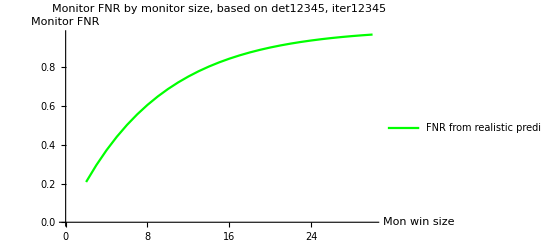

```mathematica
(* realistic prediction on aggregate detector FNR, det 12345, iter12345 *)
predFNRbyWinSizeRealUpTo30 =ListLinePlot[Assuming[{alphaPI==0.11 , pNChoPI==0 , monwin== #}, {#, Simplify@betaERSmonwin}]& /@ Table[n, {n,2,30, 1}], (* this is mon win - 1 *)
PlotLabel -> "Monitor FNR by monitor size, based on det12345, iter12345", AxesLabel -> {"Mon win size", "Monitor FNR"}, PlotStyle->Green, PlotLegends->{"FNR from realistic prediction"}]
```

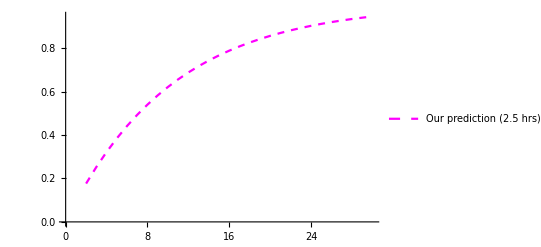

```mathematica
(* automated for session 6, det fpr 0.092478 *) 
predFNRchartSesh6 = ListLinePlot[Inner[List, Range[2,30], predMonFNRTheor[countFromFiles[ "FPcount",detFilenames[fullTripleList[{6}]]]/countFromFiles[ "h0count",detFilenames[fullTripleList[{6}]]],#]&/@ Range[2,30], List], PlotStyle->{Magenta,Dashed}, PlotLegends->{"Our prediction (2.5 hrs)"}]
```

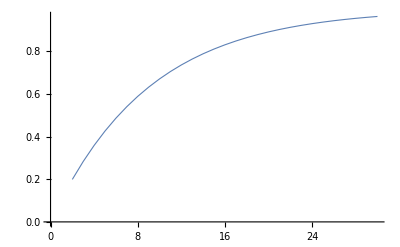

```mathematica
(* WRONG TRIPLELISTING FUNCTION!! automated for sessions 4-7, det fpr 0.106042296 *) 
predFNRchartSesh4567 = ListLinePlot[Inner[List, Range[2,30], predPrMonFNRTheor[predFPRfromData[fullStatelessTripleListNoRedun@{4,5,6,7}, detFilenames],#]&/@ Range[2,30], List], PlotStyle->{ColorData[97,"ColorList"][[1]], Thickness[0.002]}]
```

```mathematica
(*** VISUAL COMBINATIONS ***) 
(* combination of estimated and predicted FPR by win size, up to 10 on one and 5 on another*) 
Show[empFPRbyWinSizeMons12345,   predFPRbyWinSize, PlotLabel->"Empirical and predicted FPR of pipe loss monitor"]
```

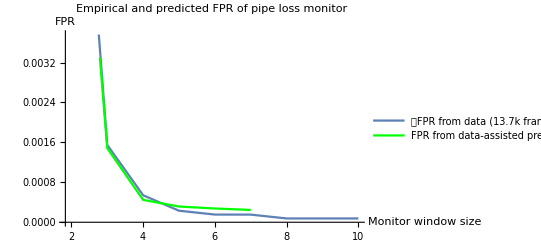

```mathematica
(* combination of estimated and predicted FNR by win size *) 
Show[empFNRbyWinSizeMons12345UpTo10, predFNRbyWinSizeCheatUpTo10, predFNRbyWinSizeRealUpTo10, PlotLabel->"Empirical and predicted FNR of pipe loss monitor, up to win of 10"]
```

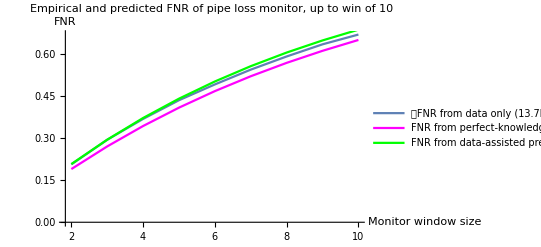

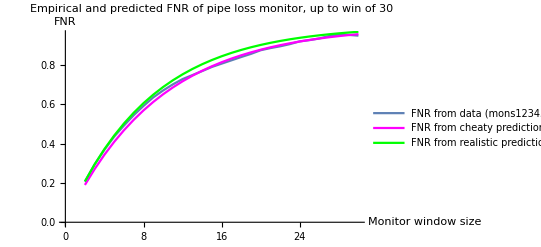

```mathematica
(* same as above for up to win = 30 *) 
Show[empFNRbyWinSizeMons12345UpTo30, predFNRbyWinSizeCheatUpTo30, predFNRbyWinSizeRealUpTo30, PlotLabel->"Empirical and predicted FNR of pipe loss monitor, up to win of 30"]
```

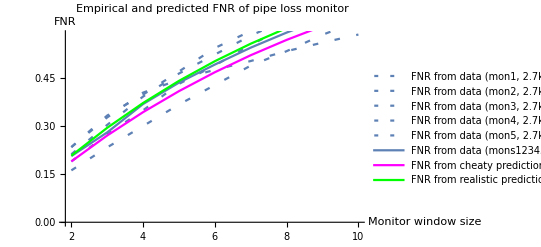

```mathematica
(* with individual empirical predictions *) 
Show[ empFNRbyWinSizeMon1, empFNRbyWinSizeMon2,  empFNRbyWinSizeMon3,empFNRbyWinSizeMon4, empFNRbyWinSizeMon5, empFNRbyWinSizeMons12345, predFNRbyWinSizeCheat, predFNRbyWinSizeReal, PlotLabel->"Empirical and predicted FNR of pipe loss monitor"]
```

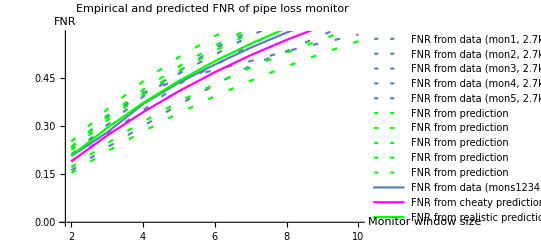

```mathematica
(* with individual theoretica predictions *) 
Show[ empFNRbyWinSizeMon1, empFNRbyWinSizeMon2,  empFNRbyWinSizeMon3,empFNRbyWinSizeMon4, empFNRbyWinSizeMon5,predFNRbyWinSizeRealDet1, predFNRbyWinSizeRealDet2,  predFNRbyWinSizeRealDet3,predFNRbyWinSizeRealDet4, predFNRbyWinSizeRealDet5, empFNRbyWinSizeMons12345, predFNRbyWinSizeCheat, predFNRbyWinSizeReal, PlotLabel->"Empirical and predicted FNR of pipe loss monitor"]
```

```mathematica
(* all together *) 
Show[ predFNRbyWinSizeRealDet1, predFNRbyWinSizeRealDet2,  predFNRbyWinSizeRealDet3,predFNRbyWinSizeRealDet4, predFNRbyWinSizeRealDet5, empFNRbyWinSizeMons12345, predFNRbyWinSizeCheat, predFNRbyWinSizeReal, PlotLabel->"Empirical and predicted FNR of pipe loss monitor"]
(*** PAIRWISE COMPARISONS OF PREDICTED AND EMPIRICAL FNRs ***)
```

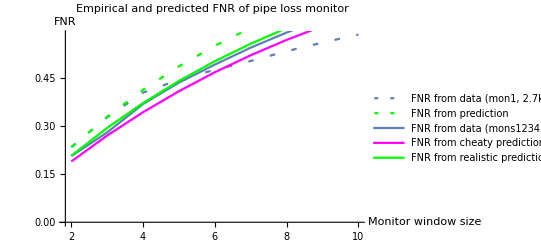

```mathematica
Show[ empFNRbyWinSizeMon1, predFNRbyWinSizeRealDet1,  empFNRbyWinSizeMons12345, predFNRbyWinSizeCheat, predFNRbyWinSizeReal, PlotLabel->"Empirical and predicted FNR of pipe loss monitor"]
```

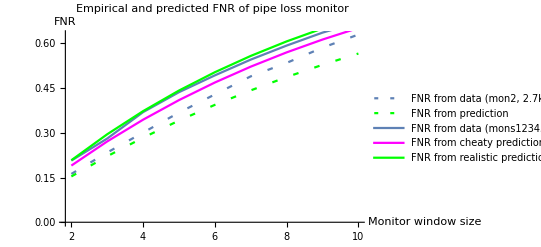

```mathematica
Show[ empFNRbyWinSizeMon2, predFNRbyWinSizeRealDet2,  empFNRbyWinSizeMons12345, predFNRbyWinSizeCheat, predFNRbyWinSizeReal, PlotLabel->"Empirical and predicted FNR of pipe loss monitor"]
```

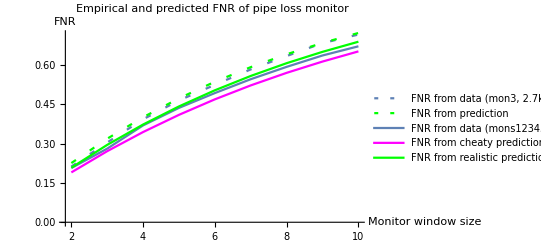

```mathematica
Show[ empFNRbyWinSizeMon3, predFNRbyWinSizeRealDet3,  empFNRbyWinSizeMons12345, predFNRbyWinSizeCheat, predFNRbyWinSizeReal, PlotLabel->"Empirical and predicted FNR of pipe loss monitor"]
```

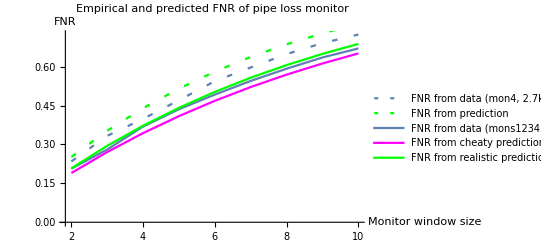

```mathematica
Show[ empFNRbyWinSizeMon4, predFNRbyWinSizeRealDet4,  empFNRbyWinSizeMons12345, predFNRbyWinSizeCheat, predFNRbyWinSizeReal, PlotLabel->"Empirical and predicted FNR of pipe loss monitor"]
```

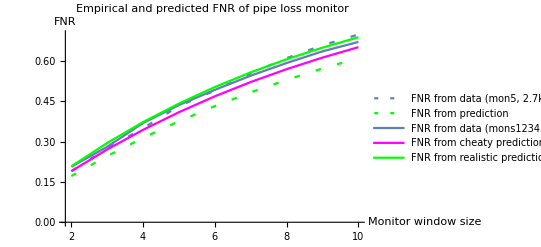

```mathematica
Show[ empFNRbyWinSizeMon5, predFNRbyWinSizeRealDet5,  empFNRbyWinSizeMons12345, predFNRbyWinSizeCheat, predFNRbyWinSizeReal, PlotLabel->"Empirical and predicted FNR of pipe loss monitor"]
```

```mathematica
(*** crossover point details: ***)
```

```mathematica
(* mon1 data: *) {{5,0.445161}, {6,0.476190},{7,0.503597}};
```

```mathematica
(* mons12345 data: *) 
mons12345vals = {{2, 0.206704} ,{3, 0.280702}, {4,0.369325},{5,0.436129},{6,0.492517},{7,0.545324},{8,0.592366},{9,0.635772},{10,0.670690}}
```

{{2,0.206704},{3,0.280702},{4,0.369325},{5,0.436129},{6,0.492517},{7,0.545324},{8,0.592366},{9,0.635772},{10,0.67069}}

```mathematica
(* cheaty prediction: *)cheatyPredVals = Assuming[{alphaPI==0.1 (* cheating a bit with alpha *) , pNChoPI==0 , monwin== #},  {#, Simplify@betaERSmonwin}]& /@ Table[n, {n,2,10, 1}]
```

{{2,0.19},{3,0.271},{4,0.3439},{5,0.40951},{6,0.468559},{7,0.521703},{8,0.569533},{9,0.61258},{10,0.651322}}

```mathematica
(* realistic prediction *) 
realPredVals = Assuming[{alphaPI==0.11 (* from estimates det 1-5, iter 1-5 *) , pNChoPI==0 , monwin== #},  {#, Simplify@betaERSmonwin}]& /@ Table[n, {n,2,10, 1}]
```

{{2,0.2079},{3,0.295031},{4,0.372578},{5,0.441594},{6,0.503019},{7,0.557687},{8,0.606341},{9,0.649644},{10,0.688183}}

```mathematica
#[[2]]&  /@Abs[mons12345vals - cheatyPredVals]
```

{0.016704,0.009702,0.025425,0.026619,0.023958,0.0236209,0.0228332,0.0231925,0.0193684}

```mathematica
#[[2]]&  /@Abs[mons12345vals - realPredVals]
```

{0.001196,0.014329,0.00325259,0.00546506,0.0105017,0.0123627,0.0139751,0.0138716,0.0174928}

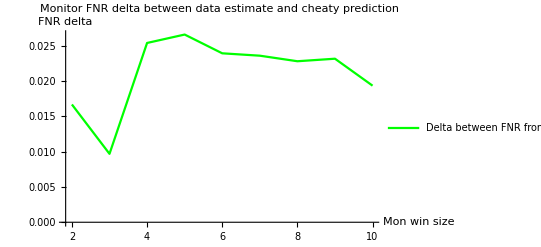

```mathematica
ListLinePlot[Transpose[{Table[n,{n,2,10,1}],#[[2]]&  /@Abs[mons12345vals - cheatyPredVals]}], (* this is mon win - 1 *)
PlotLabel -> "Monitor FNR delta between data estimate and cheaty prediction", AxesLabel -> {"Mon win size", "FNR delta"}, PlotStyle->Green, PlotLegends->{"Delta between FNR from mons12345 and cheaty prediction"}]
```

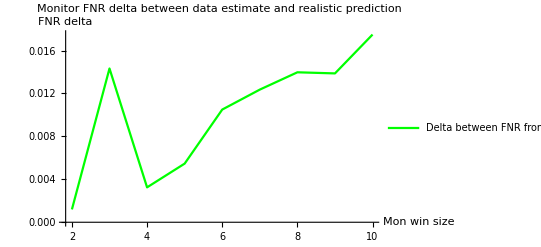

```mathematica
ListLinePlot[Transpose[{Table[n,{n,2,10,1}],#[[2]]&  /@Abs[mons12345vals - realPredVals]}], (* this is mon win - 1 *)
PlotLabel -> "Monitor FNR delta between data estimate and realistic prediction", AxesLabel -> {"Mon win size", "FNR delta"}, PlotStyle->Green, PlotLegends->{"Delta between FNR from mons12345 and realistic prediction"}]
```

```mathematica
(*** Confidence intervals ***) 
(* for detector FPR for iter 1-5. Using normal distribution assumption over the probability *)
```

```mathematica
ciWidth = 1.96/n * Sqrt[ns*nf/n]
```

(1.96 √((nf ns)/n))/n

```mathematica
(* width of PI alpha confidence interval for iter12345 *) 
Assuming[{n==1000 , ns==110 , nf== n-ns},  Simplify@ciWidth]
```

0.0193931

```mathematica
(* confidence intervals for iter12345, iter1, iter2, iter3, iter4, iter5 *) 
confInterPiAlpha = Assuming[{n==#1 , ns==#2 , nf== n-ns},  Interval[{Simplify[ns/n - ciWidth], Simplify[ns/n + ciWidth]}]]& @@@{{1000,110}, {200, 25}, {200, 16}, {200, 24}, {200, 27}, {200, 18}}
```

{Interval[{0.0906069,0.129393}],Interval[{0.0791647,0.170835}],Interval[{0.0424007,0.117599}],Interval[{0.0749626,0.165037}],Interval[{0.0876395,0.18236}],Interval[{0.0503372,0.129663}]}

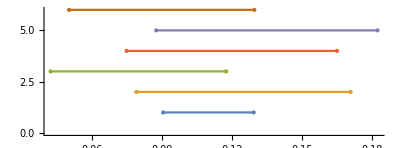

```mathematica
NumberLinePlot[confInterPiAlpha, PlotLegends->{iter12345, iter1, iter2, iter3, iter4, iter5}]
```

```mathematica
(* for FNR of PI though, the numbers are much bigger across iter 1-5 --- much tighter, 0.3% each way *) 
Assuming[{n==#1 , ns==#2 , nf== n-ns},  Interval[{Simplify[ns/n - ciWidth], Simplify[ns/n + ciWidth]}]]& @@@{{12755,1256}}
```

{Interval[{0.0933004,0.103642}]}

```mathematica
Export["~/graph.png",%744, ImageSize->2400] ;(* requires image size to be set *)
```

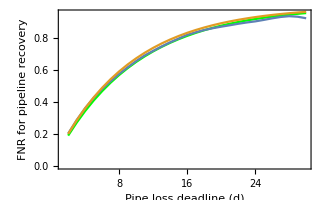

```mathematica
(* removed smaller-data charts, pre correction *) 
Show[gtFNRChart,estFNRChartSesh4567, predFNRchartSesh4567,(*PlotLabel->"Bhah",  AxesLabel -> {"Monitor window size", "Monitor FNR"}*)Frame->True, FrameLabel->{StringJoin["Pipe loss deadline ", ToString[ Style["(d)", Italic], StandardForm] ],"FNR for pipeline recovery"}, ImageSize->500, BaseStyle-> {FontSize->15}]
```

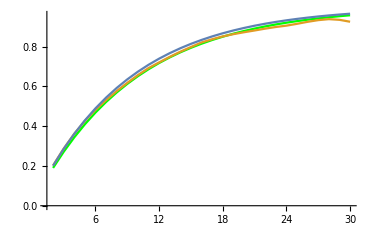

```mathematica
(* no legend *) 
Show[gtFNRChart,estFNRChartSesh4567, predFNRchartSesh4567,  ImageSize->800, BaseStyle-> {FontSize->15}]
```

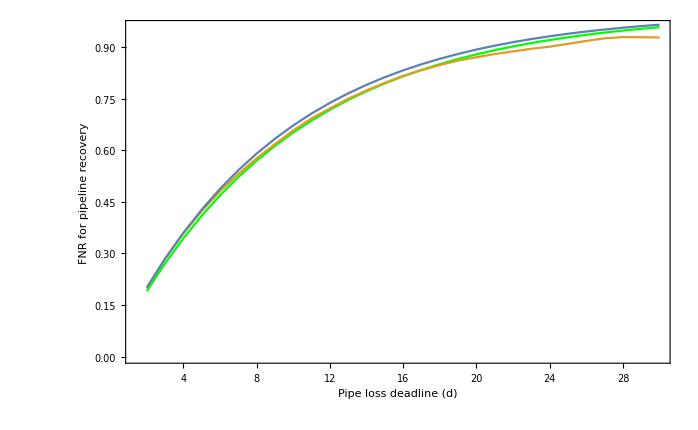

```mathematica
(* POST-CORRECTION *) 
Show[gtFNRChart,estFNRChartSesh4567, predFNRchartSesh4567,(*PlotLabel->"Bhah",  AxesLabel -> {"Monitor window size", "Monitor FNR"}*)Frame->True, FrameLabel->{StringJoin["Pipe loss deadline ", ToString[ Style["(d)", Italic], StandardForm] ],"FNR for pipeline recovery"}, ImageSize->1500, BaseStyle-> {FontSize->15}]
```

```mathematica
(* Image error calculations *) 

eccVal = {{2,0.18999999999999995},{3,0.2709999999999999},{4,0.3439},{5,0.40950999999999993},{6,0.46855899999999995},{7,0.5217030999999999},{8,0.5695327899999999},{9,0.6125795109999999},{10,0.6513215599},{11,0.6861894039099999},{12,0.7175704635189999},{13,0.7458134171670999},{14,0.7712320754503899},{15,0.794108867905351},{16,0.8146979811148158},{17,0.8332281830033342},{18,0.8499053647030008},{19,0.8649148282327007},{20,0.8784233454094307},{21,0.8905810108684876},{22,0.9015229097816388},{23,0.9113706188034749},{24,0.9202335569231275},{25,0.9282102012308147},{26,0.9353891811077333},{27,0.94185026299696},{28,0.9476652366972639},{29,0.9528987130275375},{30,0.9576088417247837}}[[All,2]];

nccVal=predPrMonFNRTheor[countFromFiles[ "FPcount",detFilenames[fullTripleList[{4,5,6,7}]]]/countFromFiles[ "h0count",detFilenames[fullTripleList[{4,5,6,7}]]],#]&/@ Range[2,30]
{2162157/10817521,10114745681/35578826569,42103434612945/117018760585441,164473814554432217/384874703565515449,617433484556373443217/1265852900026980311761,2255740267874212838125481/4163390188188738245381929,8081084263387426340912694465/13693390328952760089061164481,28526156347032416045869371190937/45037560791925627932922169978009,99551985567767560899671683026105777/148128537444643390271381017057671601,344282544033663420591003304381815241481/487194759655432110602572165102681895689,1181935826147472725757824262781931058241185/1602383564506716211771859851022720754921121,4033282297409695284664354349409325275303195257/5270239543662589620517647050013728562935566969,13694689640630242125802154022316998771280642184337/17333817859106257261882541147495153243495079761041,46304611719844043603983178911837428560600441983400681/57010926938600480134331677834111559017855317334063849,156010959327475542889531604567062425804482295430084959105/187508938701056979161816888396392917609726138711735999361,524049844070699818950152440909845999127361883288282341465177/616716899387776404463215745935736306018389270222899701898329,1755755405343557279700084344996467427621079737401472845149270897/2028381882086396594279516588382636710494482309763117119543604081,5869280915604725135092640399148382110602801948922934750910785595081/6671348010182158398585330059190492140816352316810892206178913822409,19582382213242310311751657584833640942256717587664653632723614317104225/21942063605489118972947150564677528651144982769991024466122447561903201,65225264542463601220786037860523674094066572164096296477217362624901040697/72167447198453712302023178207224391733615848330500479469076730031099628089,216934832461791352960354566223567513116308554677454970611743106163250432677457/237358733835714259761354233123561024411862525159016076973793365072286676784721,720585757743583008546553052723611299059096064091251102249654516012366249781376681/780672875585664200355094072743392209290615845248003877166806377722750879944947369,2390856787109846688667176724354821538455704318857518088195365399178176062197706932545/2567633087801249554967904405253016976356835515020684752001626176330127644138931896641,7924869349144202553632696751674681856932504029790995824415329287568748267501863163681817/8444945225778309786289437588877172835237632008903032149333348493949789821572947008052249,26245361618527317408629828686767292996922885162734461871248570691427834471076294039346036017/27775424847584860887105960229817021455096571677282072739157383196600858723153422709483846961,86851926303819314544014724196215882441865638520781666065700906943401186990840694743946932857481/91353372323706607457691503195868183565812624246580737239088633333620224340451607291492372654729,287217987382162616176310270194233385841305689141703177387255823994252509973190031666839729777900065/300461241572671031928347354011210455747957721147004044779362515034276917855745336381718413661403681,949255369704039264869841346753324649289662666692901151411745426907984974837068704888298774547089068537/988217023532515024012334447342871188955032944852496303279323311947736782827546411359471862532356706809,3135620604835066230579353295376257420777583997274331404691280235209156459611814734523111731016263816898577/3250245790398441913976567997310703340473103355619860341485694372996106278719800146961302955868921208694801}
```

```mathematica
bbcVal = {0.201276,0.284999,0.358476,0.423147,0.480576,0.53085,0.576453,0.61784,0.65734,0.692441,0.721449,0.749419,0.77381,0.795633,0.816231,0.8325,0.847522,0.860479,0.870064,0.879467,0.887072,0.894829,0.900802,0.908985,0.917598,0.925217,0.928571,0.928328,0.927632};
```

```mathematica
Mean@((eccVal-nccVal)^2)
```

0.000243471

```mathematica
Sqrt@Mean@((eccVal-nccVal)^2)
```

0.0156036

```mathematica
Mean@((eccVal-bbcVal)^2)
```

0.0001741

```mathematica
Sqrt@Mean@((eccVal-bbcVal)^2)
```

0.0131947

```mathematica
Mean@(Abs[(eccVal-nccVal)])
```

0.0149515

```mathematica
Mean@(Abs[(eccVal-bbcVal)])
```

0.0109296

```mathematica
(*** production-ready, but with wrong triples ***)
```

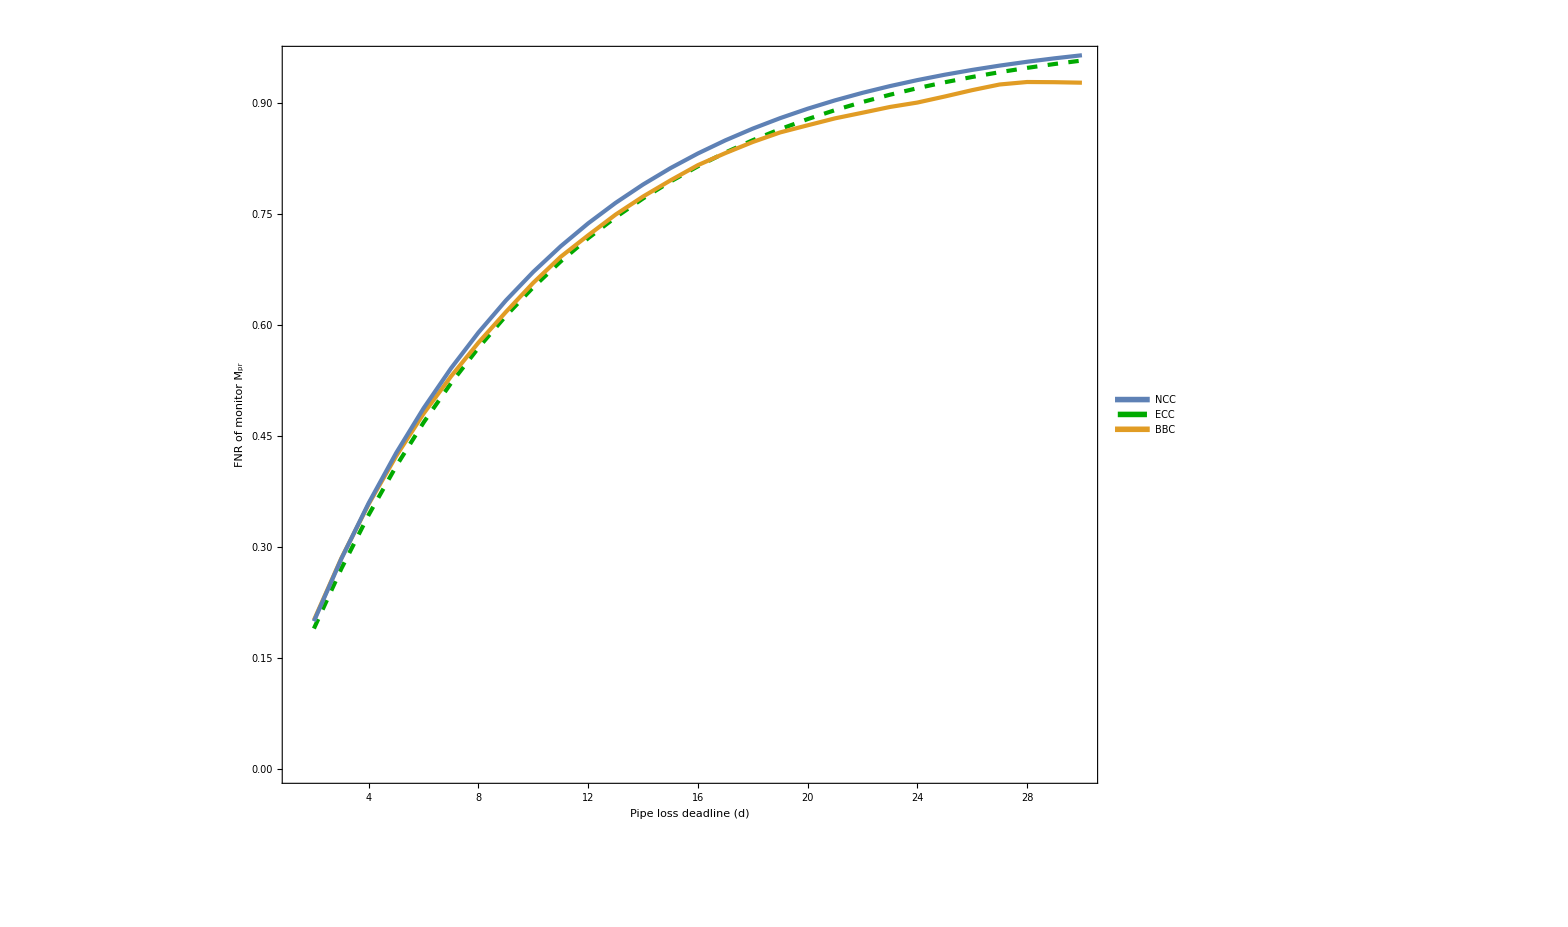

```mathematica
Legended[Show[gtFNRChart,estFNRChartSesh4567, predFNRchartSesh4567,(*PlotLabel->"Bhah",  AxesLabel -> {"Monitor window size", "Monitor FNR"}*)Frame->True, FrameLabel->{StringJoin["Pipe loss deadline ", ToString[ Style["(d)", Italic], StandardForm] ],StringJoin["FNR of monitor ", ToString[Style[Subscript[ "M", "pr"],Italic], StandardForm]]}, ImageSize->1500, BaseStyle-> {FontSize->35}], 
Placed[LineLegend[Directive@@@{{ColorData[97,"ColorList"][[1]],AbsoluteThickness[5]},{AbsoluteDashing[10],AbsoluteThickness[5],Darker@Green} , {ColorData[97,"ColorList"][[2]],AbsoluteThickness[5]}},{"NCC","ECC", "BBC"}
(*, LegendMarkers->Graphics[{ Thickness[0.3],Line[{{-10,0},{10,0}}]}]*)(*LegendMarkers->Automatic*)],{0.1,0.85}]]
```

```mathematica
(* production-ready but with proper tripling function *)
```

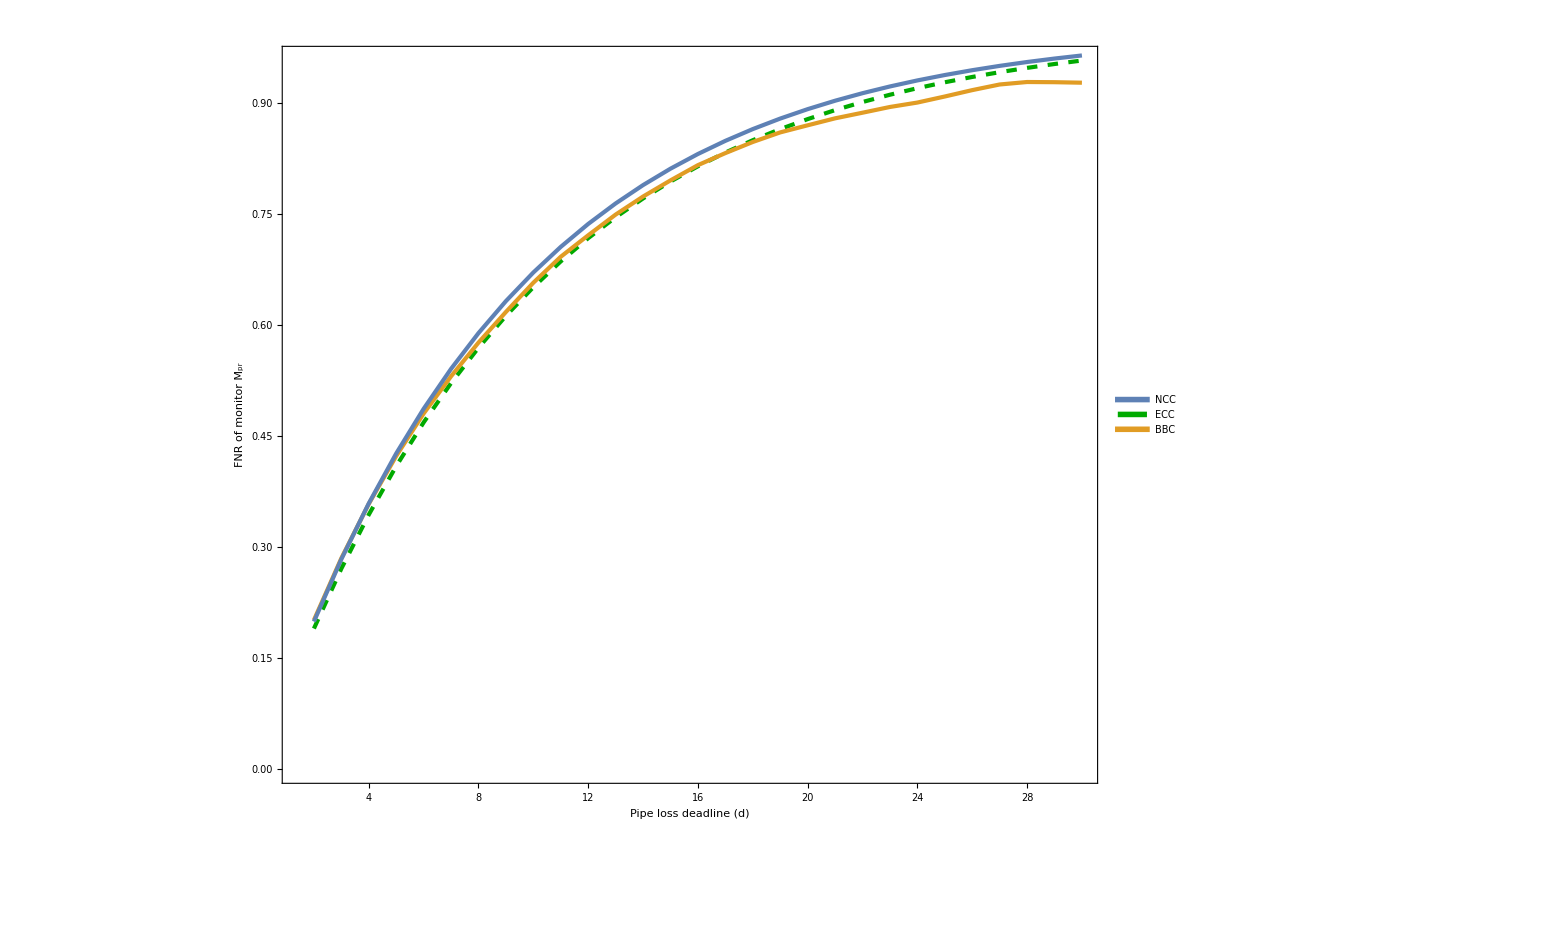

```mathematica
Legended[Show[gtFNRChart,estFNRChartSesh4567, predFNRchartSesh4567,(*PlotLabel->"Bhah",  AxesLabel -> {"Monitor window size", "Monitor FNR"}*)Frame->True, FrameLabel->{StringJoin["Pipe loss deadline ", ToString[ Style["(d)", Italic], StandardForm] ],StringJoin["FNR of monitor ", ToString[Style[Subscript[ "M", "pr"],Italic], StandardForm]]}, ImageSize->1500, BaseStyle-> {FontSize->35}], 
Placed[LineLegend[Directive@@@{{ColorData[97,"ColorList"][[1]],AbsoluteThickness[5]},{AbsoluteDashing[10],AbsoluteThickness[5],Darker@Green} , {ColorData[97,"ColorList"][[2]],AbsoluteThickness[5]}},{"NCC","ECC", "BBC"}
(*, LegendMarkers->Graphics[{ Thickness[0.3],Line[{{-10,0},{10,0}}]}]*)(*LegendMarkers->Automatic*)],{0.1,0.85}]]
```

```mathematica
(* RMSE ESTIMATES ON FULL DATASET *)
```

```mathematica
bbcPrEsts = getMonValues[dataDirPathForSeshNumPostCorr[All], "FNR"]
```

{0.201409,0.284999,0.358476,0.423147,0.480576,0.53085,0.576453,0.61784,0.65734,0.692441,0.721449,0.749419,0.77381,0.795633,0.816231,0.8325,0.847522,0.860479,0.870064,0.879467,0.887072,0.894829,0.900802,0.908985,0.917598,0.925217,0.928571,0.928328,0.927632}

```mathematica
nccPrEsts = N@predPrMonFNRTheor[predFPRfromData[fullStatelessTripleListNoRedun@{4,5,6,7}, detFilenames],#]&/@ Range[2,30]
```

{0.199446,0.283715,0.359113,0.426575,0.486936,0.540942,0.589264,0.6325,0.671184,0.705796,0.736765,0.764474,0.789266,0.811449,0.831296,0.849054,0.864943,0.87916,0.89188,0.903261,0.913444,0.922555,0.930707,0.938001,0.944527,0.950367,0.955591,0.960266,0.964448}

```mathematica
eccPrEsts = Assuming[{alphaPI==0.1 (* cheating a bit *) , pNChoPI==0 , monwin== #}, Simplify@betaERSmonwin]& /@ Table[n, {n,2,30, 1}]
```

{0.19,0.271,0.3439,0.40951,0.468559,0.521703,0.569533,0.61258,0.651322,0.686189,0.71757,0.745813,0.771232,0.794109,0.814698,0.833228,0.849905,0.864915,0.878423,0.890581,0.901523,0.911371,0.920234,0.92821,0.935389,0.94185,0.947665,0.952899,0.957609}

```mathematica
bbcRmse = Sqrt@Mean[(eccPrEsts - bbcPrEsts)^2 ]
```

0.0131986

```mathematica
nccRmse = Sqrt@Mean[(eccPrEsts - nccPrEsts)^2 ]
```

0.0149465